# Ejercicio : Validez de un string en una GIC

Estudiante : Andrey Arguedas Espinoza - 2020426569

## Explicación (solución)

Construiremos una función que valide un string en una GIC con un metodo que mejore el rendimiento del método visto en clase.
Para esto utilizaremos  el metodo de la derivación, para esto mediante un string dado aplicaremos el siguiente pseudocodigo:
Supongamos que recibimos el string a*(a+b00)
- Tomamos el primer carácter del string de Izquierda a Derecha “a”
- Mediante las reglas de Producción revisamos si es posible llegar a “a”; Si hay forma de llegar y no es el ultimo carácter del String insertamos “a” en un acumulador
- Si tenemos símbolos como “*” o “+” debemos hacer un split en el símbolo y aplicar sobre el string acumulador lo siguiente “a*E”
- Si hay paréntesis debemos pasar al string acumulador (E) por ejemplo : “a*(E)”
- Finalmente si el String acumulador es igual a la expresión original el string inicial es validado.

## Código

```mathematica
rulesSet={
"E"-> "I",
"E"-> "E+E",
"E"-> "E*E",
"E"-> "(E)",
"I"->"a",
"I"->"b",
"I"->"Ia",
"I"->"Ib",
"I"->"I0",
"I"->"I1"
}
```

{E→I,E→E+E,E→E*E,E→(E),I→a,I→b,I→Ia,I→Ib,I→I0,I→I1}

```mathematica
ProductionRule[s0_,rules_,n_]:=Union[Flatten[NestList[Flatten[StringReplaceList[#,rules]]&,s0,n]]];
```

```mathematica
derivativeMethod[start_, expression_, rules_] := NestWhileList[StringReplaceList[#,rules]&,start,expression]
```

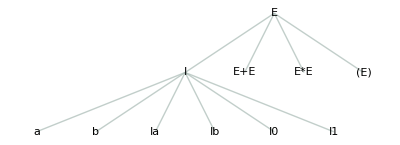

```mathematica
myTree = RulesTree["E" -> { "I" -> {"a", "b","Ia","Ib","I0","I1"},"E+E","E*E","(E)"}]
```

```mathematica
TreePosition[myTree, "a"]
```

{{1,1}}

```mathematica
TreeExpression[myTree]
```

E[I[a,b,Ia,Ib,I0,I1],E+E,E*E,(E)]

```mathematica
rulesSetSimplified={
"E"-> "I",
"E"-> "E+E",
"E"-> "E*E",
"E"-> "(E)",
"I"->"a",
"I"->"b",
"I"->"0",
"I"->"1"
}
```

{E→I,E→E+E,E→E*E,E→(E),I→a,I→b,I→0,I→1}

```mathematica
Characters["a*(a+b00)"]
```

{a,*,(,a,+,b,0,0,)}

```mathematica
Fold[f,x, Characters["a*(a+b00)"]]
```

f[f[f[f[f[f[f[f[f[x,a],*],(],a],+],b],0],0],)]

```mathematica
acumulatorString = ""
```

```mathematica
Thread[validateString[Characters["a*(a+b00)"],acumulatorString, "hola"]]
```

a*(a+b00)

```mathematica
validateString[currentCharacter_, acumulator_, randomString_]:= StringJoin[acumulator,StringJoin[acumulator,currentCharacter]];
```

```mathematica
Select[rulesSetSimplified,#>"0"&]
```

{}

```mathematica
TreeRules[rulesSetSimplified]
```

TreeRules::tree: Tree expected at position 1 in TreeRules[{E→I,E→E+E,E→E*E,E→(E),I→a,I→b,I→0,I→1}].

TreeRules[{E→I,E→E+E,E→E*E,E→(E),I→a,I→b,I→0,I→1}]

```mathematica
RulesTree[rulesSetSimplified]
```

```mathematica
Clear[EmptyQ]
```

## Codigo

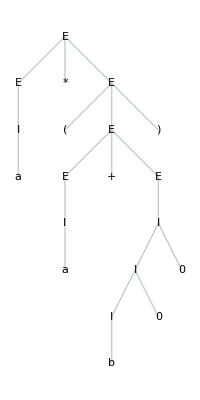

```mathematica
experimentTree = RulesTree["E"->{"E" -> {"I"-> {"a"}}, "*", "E" ->{"(", "E" ->{"E"-> {"I"-> {"a"}}, "+", "E" -> {"I" -> {"I" -> {"I" -> {"b"}, "0"}, "0"}}}, ")"}}]
```

```mathematica
TreeLeaves[experimentTree]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}